# Doppler Cooling

After ions are loaded into a trap they are confined along the axis of the trap but, as shown in the previous notebook, they can execute harmonic motion in the x y plane. Our goal is to align ions along the axis and minimize x y motion as much as possible. This is achieved by requiring small values for the parameters v_ox,  v_oy, the initial velocity of an ion. Since velocity can be related to kinetic energy, which in turn, is characterized by a temperature, the process of minimizing the kinetic energy of the trapped ion is called cooling.  Laser cooling, described below, is a powerful method for achieving the latter.

Atoms and ions have internal structure called energy levels, and in an over simplistic description we can consider our ions to have two energy levels as shown in the picture below

-Graphics-

## Lorentzian Profile

In the discussion above we introduced the function N(ω) which  denotes the number of photons emitted, by spontaneous emission, per unit time. We provide a plot of this functions below

```mathematica
ClearAll["Global`*"]
(* For the purpose of plotting, we arbitrarly the function parameters to arbitrary numerical values *)
parameters={n0->10,ω0->3,Γ->0.2,ℏ->1,c->10,mass->1};
nphotons[ω_]= n0 (Γ/2)^2/((ω-ω0)^2+(Γ/2)^2)
```

(n0 Γ^2)/(4 (Γ^2/4+(ω-ω0)^2))

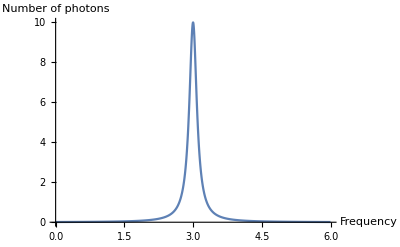

```mathematica
Plot[nphotons[ω]/. parameters,{ω,0,6},PlotRange->All,AxesLabel->{Frequency,"Number of photons"}]
```

The function N(ω) is highly peaked near the resonance frequency ω_0 and the width of the curve is determined by the parameter Γ ,  the full width at half maximum (FWHM). This type of function is called a Lorentzian and the parameters, characterizing it, depend on the properties of the ion.Though N(ω) determines the fluorescence spectrum, it also determines the efficiency in which a photon of frequency ω can be absorbed by the ion. The closer ω is to the resonance frequency  the more likely the ion will absorb the photon.

The total number of photons emitted, summed over all frequencies, is given by the the integral  ∫N(ω) ⅆω.

```mathematica
?Integrate
```

RowBox[{"Integrate", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["x", "TI"]}], "]"}] gives the indefinite integral RowBox[{"∫", StyleBox["f", "TI"], " ", StyleBox["d", "TI"], StyleBox["x", "TI"]}]. 
RowBox[{"Integrate", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] gives the definite integral RowBox[{SubsuperscriptBox["∫", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]], " ", StyleBox["f", "TI"], " ", StyleBox["d", "TI"], StyleBox["x", "TI"]}]. 
RowBox[{"Integrate", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] gives the multiple integral RowBox[{SubsuperscriptBox["∫", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]], RowBox[{StyleBox["d", "TI"], StyleBox["x", "TI"], RowBox[{SubsuperscriptBox["∫", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]], RowBox[{StyleBox["d", "TI"], "", StyleBox["y", "TI"], " ", "…", " ", StyleBox["f", "TI"]}]}]}]}]. 
RowBox[{"Integrate", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}], "∈", StyleBox["reg", "TI"]}]}], "]"}] integrates over the geometric region StyleBox["reg", "TI"].

```mathematica
"N(ω_0)" Integrate[(Γ/2)^2/((ω-ω0)^2+(Γ/2)^2),{ω,-∞,∞},Assumptions->ω0>0 && Γ>0]
```

(N(ω_0) π Γ)/2

Or,
∫N(ω) ⅆω =N(ω_0)(π Γ)/2.

## Doppler shifted force

Since the ion experiences the laser beam with the Doppler shifted frequency
ω_shift=ω √((1-v/c)/(1+v/c))
we insert that value into the expression for the radiation force

```mathematica
radiationForce= ℏ ω √(1-v/c)/√(1+v/c)/c  nphotons[ω√(1-v/c)/√(1+v/c)]
```

(n0 √(1-v/c) Γ^2 ω ℏ)/(4 c √(1+v/c) (Γ^2/4+((√(1-v/c) ω)/(√(1+v/c))-ω0)^2))

Lets define the parameter γ ≡ v/c  <<1

```mathematica
Force[ω_]=radiationForce /. v/c->γ
```

(n0 √(1-γ) Γ^2 ω ℏ)/(4 c √(1+γ) (Γ^2/4+((√(1-γ) ω)/(√(1+γ))-ω0)^2))

Since γ << 1 we expand the expression for the radiation force to terms linear in γ.

```mathematica
approximation=Normal[Series[Force[ω],{γ,0,1}]]
```

-(n0 γ Γ^2 ω (Γ^2-4 ω^2+4 ω0^2) ℏ)/(c (Γ^2+4 ω^2-8 ω ω0+4 ω0^2)^2)+(n0 Γ^2 ω ℏ)/(c (Γ^2+4 ω^2-8 ω ω0+4 ω0^2))

```mathematica
?Series
```

RowBox[{"Series", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]], ",", StyleBox["n", "TI"]}], "}"}]}], "]"}] generates a power series expansion for StyleBox["f", "TI"] about the point RowBox[{StyleBox["x", "TI"], "=", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}] to order SuperscriptBox[RowBox[{"(", RowBox[{StyleBox["x", "TI"], "-", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], ")"}], StyleBox["n", "TI"]]. 
RowBox[{"Series", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["x", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] successively finds series expansions with respect to StyleBox["x", "TI"], then StyleBox["y", "TI"], etc.

The radiation force is a sum of two components, a velocity independent contribution that we label f_0, and the term  f_1  which is a linear function of the ion velocity.

```mathematica
(* f0 is velocity independent *) 
f0[ω_,v_]=FullSimplify[(n0 Γ^2 ω ℏ)/(c (Γ^2+4 ω^2-8 ω ω0+4 ω0^2))]
(* f1 depends linearly on the velocity *)
f1[ω_,v_]=FullSimplify[-(n0 γ Γ^2 ω (Γ^2-4 ω^2+4 ω0^2) ℏ)/(c (Γ^2+4 ω^2-8 ω ω0+4 ω0^2)^2)] /. γ->v/c
```

(n0 Γ^2 ω ℏ)/(c (Γ^2+4 (ω-ω0)^2))

-(n0 v Γ^2 ω (Γ^2-4 ω^2+4 ω0^2) ℏ)/(c^2 (Γ^2+4 (ω-ω0)^2)^2)

Let’s plot the velocity dependent term as a function of frequency ω, and ion velocity ν (in 1D)

```mathematica
Plot3D[f1[ω,v] /. parameters,{ω,2,4},{v,-1,1},PlotRange->All,PlotPoints->50,AxesLabel->{Frequency, "Ion velocity"}]
```

-Graphics3D-

This figure demonstrates how, near the resonance frequency, the ion experiences a force that changes sign as the velocity of the ion changes sign. It is this component that provides the damping parameter β given in the discussion above, and which allows cooling of the ion.

### Ion Dynamics and Cooling

The explore the effects the total radiation pressure force on the ion we solve for the ions equation of motion as given by Newtons, force law.
Our model is restricted to 1D motion. Below we define the total radiation force by the function frad[ω,t].

```mathematica
frad[ω_,t_]:= ℏ ω/c √(1-x'[t]/c)/√(1+x'[t]/c)  nphotons[ω√(1-x'[t]/c)/√(1+x'[t]/c)] /mass  /. parameters
(* Here, x'[t] denotes the velocity of the ion, and we use the parameters discussed above *)
```

First, we integrate the equations of motion when the laser field is off, and the ion is subjected to a harmonic restoring force proportional to the parameter Ω.

InterpolatingFunction[{{0., 100.}}, <>][t]

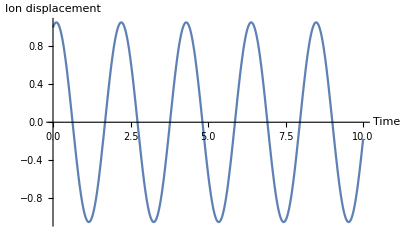

```mathematica
(* The harmonic restoring force is proportional to the parameter Ω whose numerical value is given by the variable Omega *)
Omega=3;
(* x0 is the initial position of the ion, and v0 is the initial velocity*)
x0=1;
v0=1;
sols=Flatten[NDSolve[ {x''[t] == - Omega^2 x[t],x[0]==x0,x'[0]==v0},x[t],{t,0,100}]];
x1[t_] = x[t] /. sols
Plot[x1[t],{t,0,10},AxesLabel->{"Time"," Ion displacement"}]
```

With the laser shut off, the ion undergoes simple harmonic motion. Let’s now turn the laser on at a frequency several far away from resonance, i.e. ω = ω_0- 5 Γ

InterpolatingFunction[{{0., 100.}}, <>][t]

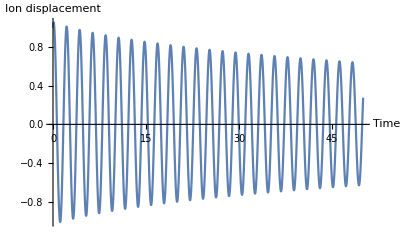

```mathematica
(* Laser frequency *)
omega=ω0 -5Γ/. parameters;
sols=Flatten[NDSolve[ {x''[t] == - Omega^2 x[t]+ frad[omega,t],x[0]==x0,x'[0]==v0},x[t],{t,0,100}]];
x1[t_] = x[t] /. sols
Plot[x1[t],{t,0,50},AxesLabel->{"Time"," Ion displacement"}]
```

In this figure we notice a slow attenuation of the ion’s displacement from the origin for larger values of t.  In order to enhance this attenuation we adjust the laser frequency to a value closer to ω_0 .

InterpolatingFunction[{{0., 100.}}, <>][t]

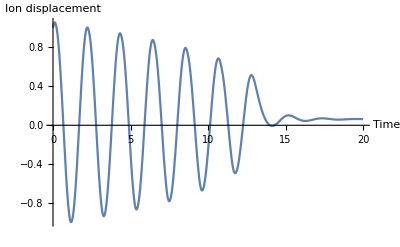

```mathematica
(* Laser frequency *)
omega=ω0 - Γ  /. parameters;
sols=Flatten[NDSolve[ {x''[t] == - Omega^2 x[t]+ frad[omega,t],x[0]==x0,x'[0]==v0},x[t],{t,0,100}]];
x1[t_] = x[t] /. sols
Plot[x1[t],{t,0,20},AxesLabel->{"Time"," Ion displacement"}]
```

In this figure the harmonic motion is attenuated at around t=15, after which the ion is almost stationary at it’s equilibrium position 

x_s = (ℏ ω N(ω))/(m c Ω^2)
On other words the harmonic motion of the trapped ions have been suppressed, an we are now in possession of an almost stationary ion.  
Below we show an image of several trapped ions in such a trap.